```mathematica
c2=0.54;
c1=1.4;
Dc=0.76;
Fc=0.5;
fc=0.093;
```

```mathematica
(*pi+result*)
```

```mathematica
gpdu=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-u-up-xi1-pi-noD.wdx"];
Hdgu=Query[1,1]@gpdu;
Heru=Query[1,2]@gpdu;
Hdau=Query[1,3]@gpdu;
Edgu=Query[2,1]@gpdu;
Eeru=Query[2,2]@gpdu;
Edau=Query[2,3]@gpdu;
Hdgf=Interpolation[Flatten[Hdgu,1]];
Herf=Interpolation[Flatten[Heru,1]];
Hdaf=Interpolation[Flatten[Hdau,1]];
Edgf=Interpolation[Flatten[Edgu,1]];
Eerf=Interpolation[Flatten[Eeru,1]];
Edaf=Interpolation[Flatten[Edau,1]];
dgpdu=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-u-dleta-pi-xi1.wdx"];
dHdgu=Query[1,1]@dgpdu;
dHeru=Query[1,2]@dgpdu;
dHdau=Query[1,3]@dgpdu;
dEdgu=Query[2,1]@dgpdu;
dEeru=Query[2,2]@dgpdu;
dEdau=Query[2,3]@dgpdu;

dHdaf=Interpolation[Flatten[dHdau,1]];
dEdaf=Interpolation[Flatten[dEdau,1]];
Dgpdu=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-u-D-xi1-pi.wdx"];

DHeru=Query[1,2]@Dgpdu;
DHdau=Query[1,3]@Dgpdu;

DEeru=Query[2,2]@Dgpdu;
DEdau=Query[2,3]@Dgpdu;

DHerf=Interpolation[Flatten[DHeru,1]];
DHdaf=Interpolation[Flatten[DHdau,1]];

DEerf=Interpolation[Flatten[DEeru,1]];
DEdaf=Interpolation[Flatten[DEdau,1]];
dDgpdu=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-u-dleta-D-pi-xi1.wdx"];

dDHeru=Query[1,2]@dDgpdu;
dDHdau=Query[1,3]@dDgpdu;

dDEeru=Query[2,2]@dDgpdu;
dDEdau=Query[2,3]@dDgpdu;

dDHdaf=Interpolation[Flatten[dDHdau,1]];

dDEdaf=Interpolation[Flatten[dDEdau,1]];
```

```mathematica
Hdgall[x_,t_]:=Hdgf[x,t];
Herall[x_,t_]:=Herf[x,t]+Hdaf[x,t]+dHdaf[x,t]+DHerf[x,t]+DHdaf[x,t]+dDHdaf[x,t];
Edgall[x_,t_]:=Edgf[x,t];
Eerall[x_,t_]:=Eerf[x,t]+Edaf[x,t]+dEdaf[x,t]+DEerf[x,t]+DEdaf[x,t]+dDEdaf[x,t];
```

```mathematica
(*u quark*)
```

```mathematica
(*pi+,只需要乘上系数*)
Coep1=(-2*0.76)^2/(6*2*(0.093)^2*(2Pi)^4);
p1Hdg[x_,t_]=Coep1*Hdgall[x,t];
p1Her[x_,t_]=Coep1*Herall[x,t];

p1Edg[x_,t_]=Coep1*Edgall[x,t];
p1Eer[x_,t_]=Coep1*Eerall[x,t];

(*pi0,先系数，求和之后整体反转*)
mp0=(-2*0.76)^2/(3*2*2*(0.093)^2*(2Pi)^4);
(*pi0的u，之后要和反转的求和*)
p0Hdg[x_,t_]=mp0*Hdgall[x,t];
p0Her[x_,t_]=mp0*Herall[x,t];

p0Edg[x_,t_]=mp0*Edgall[x,t];
p0Eer[x_,t_]=mp0*Eerall[x,t];
(*反转*)
p0Hdg0[x_,t_]=-p0Hdg[-x,t];
p0Her0[x_,t_]=-p0Her[-x,t];
p0Edg0[x_,t_]=-p0Edg[-x,t];
p0Eer0[x_,t_]=-p0Eer[-x,t];
(*求和,只有erbl要加起来，以及画图也是分段那其实只要算erbl*)
p0Herre[x_,t_]=p0Her[x,t]+p0Her0[x,t];
p0Eerre[x_,t_]=p0Eer[x,t]+p0Eer0[x,t];

(*pi-,只需要乘上系数*)
mp11=(-2*0.76)^2/(2*2*(0.093)^2*(2Pi)^4);
p11Hdg[x_,t_]=mp11*Hdgall[x,t];
p11Her[x_,t_]=mp11*Herall[x,t];

p11Edg[x_,t_]=mp11*Edgall[x,t];
p11Eer[x_,t_]=mp11*Eerall[x,t];

(*pi-的u贡献,ubar的反转*)
p11Hdgre[x_,t_]=-p11Hdg[-x,t];
p11Herre[x_,t_]=-p11Her[-x,t];
p11Edgre[x_,t_]=-p11Edg[-x,t];
p11Eerre[x_,t_]=-p11Eer[-x,t];
(*总结果*)
Hdgzall[x_,t_]=p1Hdg[x,t]+p0Hdg[x,t];
Hdgfall[x_,t_]=p0Hdg0[x,t]+p11Hdgre[x,t];
Herallwhole[x_,t_]=p1Her[x,t]+p0Herre[x,t]+p11Herre[x,t];
Edgzall[x_,t_]=p1Edg[x,t]+p0Edg[x,t];
Edgfall[x_,t_]=p0Edg0[x,t]+p11Edgre[x,t];
Eerallwhole[x_,t_]=p1Eer[x,t]+p0Eerre[x,t]+p11Eerre[x,t];
```

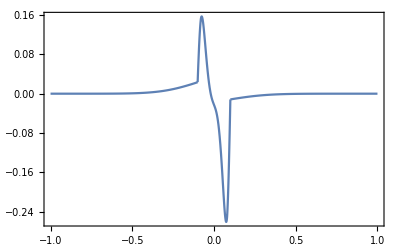
-Graphics-H_uxdiagram u

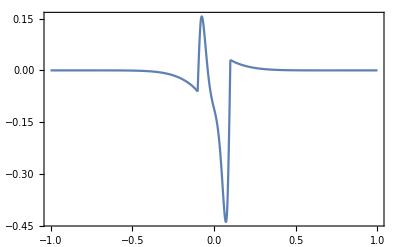
-Graphics-E_uxdiagram u

```mathematica
pHu2d=Labeled[Show[Plot[I*Hdgzall[x,-1],{x,0.1,1},PlotRange->All],Plot[-I*Hdgfall[x,-1],{x,-1,-0.1},PlotRange->All],Plot[I*Herallwhole[x,-1],{x,-0.1,0.1},PlotRange->All],Frame->True,FrameStyle->Directive[Thick,20]],
{"H_u","x","diagram u"},{Left,Bottom,Top},LabelStyle->24]
pEu2d=Labeled[Show[Plot[I*Edgzall[x,-1],{x,0.1,1},PlotRange->All],Plot[-I*Edgfall[x,-1],{x,-1,-0.1},PlotRange->All],Plot[-I*Eerallwhole[x,-1],{x,-0.1,0.1},PlotRange->All],Frame->True,FrameStyle->Directive[Thick,20]],
{"E_u","x","diagram u"},{Left,Bottom,Top},LabelStyle->24]
```

```mathematica
(*d quark*)
```

```mathematica
(*npi+,dbar=u，所以之后再对dbar反转得到d*)
(*pi+的dbar贡献就是u，反转*)
p1Hdgd[x_,t_]=-p1Hdg[-x,t];
p1Herd[x_,t_]=-p1Her[-x,t];

p1Edgd[x_,t_]=-p1Edg[-x,t];
p1Eerd[x_,t_]=-p1Eer[-x,t];
```

```mathematica
(*pi0,u=d，所以直接套用u的形式*)
```

```mathematica
(*pi-,ubard,所以不再反转*)
```

```mathematica
(*总结果*)
Hdgzalld[x_,t_]=p0Hdg[x,t]+p11Hdg[x,t];
Hdgfalld[x_,t_]=p1Hdgd[x,t]+p0Hdg0[x,t];
Herallwholed[x_,t_]=p1Herd[x,t]+p0Herre[x,t]+p11Her[x,t];
Edgzalld[x_,t_]=p0Edg[x,t]+p11Edg[x,t];
Edgfalld[x_,t_]=p1Edgd[x,t]+p0Edg0[x,t];
Eerallwholed[x_,t_]=p1Eerd[x,t]+p0Eerre[x,t]+p11Eer[x,t];
```

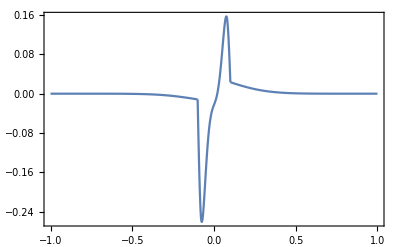
-Graphics-H_dxdiagram u

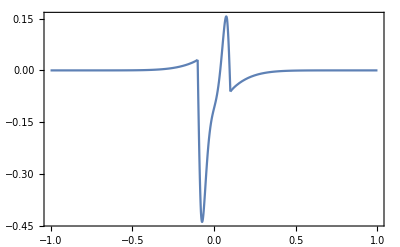
-Graphics-E_dxdiagram u

```mathematica
pHd2d=Labeled[Show[Plot[I*Hdgzalld[x,-1],{x,0.1,1},PlotRange->All],Plot[I*Hdgfalld[x,-1],{x,-1,-0.1},PlotRange->All],Plot[I*Herallwholed[x,-1],{x,-0.1,0.1},PlotRange->All],Frame->True,FrameStyle->Directive[Thick,20]],
{"H_d","x","diagram u"},{Left,Bottom,Top},LabelStyle->24]
pEd2d=Labeled[Show[Plot[I*Edgzalld[x,-1],{x,0.1,1},PlotRange->All],Plot[I*Edgfalld[x,-1],{x,-1,-0.1},PlotRange->All],Plot[I*Eerallwholed[x,-1],{x,-0.1,0.1},PlotRange->All],Frame->True,FrameStyle->Directive[Thick,20]],
{"E_d","x","diagram u"},{Left,Bottom,Top},LabelStyle->24]
```